```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="8";
p="0.1";
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1-low.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

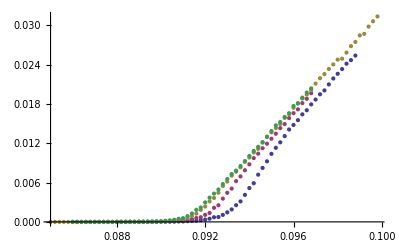

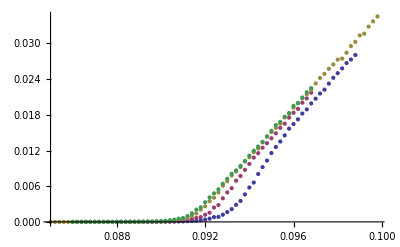

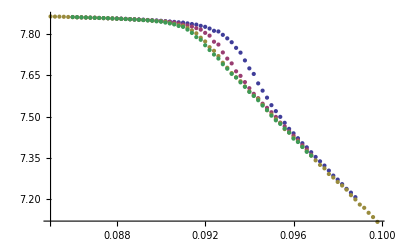

```mathematica
v="8";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="0";
nvel="0";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v8=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v8=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v8=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v8=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v8=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v8=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v8=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v8=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v8=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v8=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v8=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v8=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];


ListPlot[{gap5v8,gap10v8,gap20v8,gap30v8},PlotRange->Full]
ListPlot[{vel5v8,vel10v8,vel20v8,vel30v8},PlotRange->Full]
ListPlot[{avel5v8,avel10v8,avel20v8,avel30v8}]
```

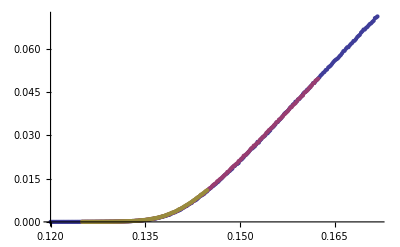

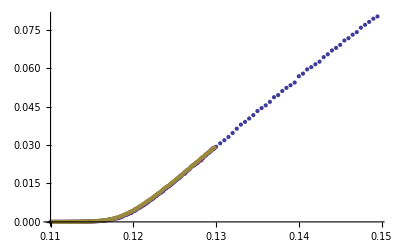

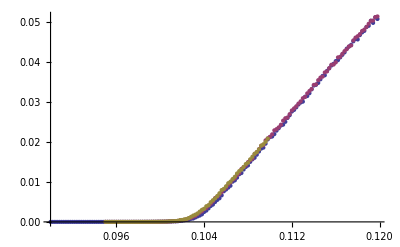

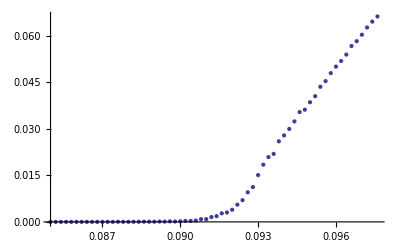

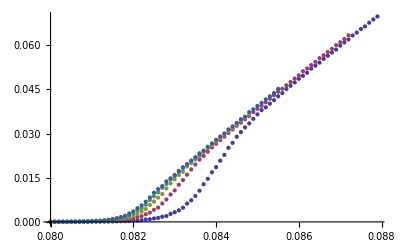

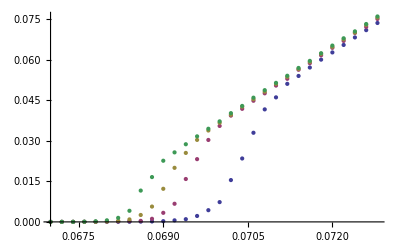

```mathematica
ListPlot[{gap10v5,gap20v5,gap40v5},PlotRange->Full]
ListPlot[{gap10v6,gap20v6,gap30v6}]
ListPlot[{gap10v7,gap20v7,gap30v7},PlotRange->Full]
ListPlot[{gap10v8}]
ListPlot[{gap10v9,gap20v9,gap30v9,gap40v9,gap50v9}]
ListPlot[{gap10v11,gap20v11,gap30v11,gap50v11}]
```

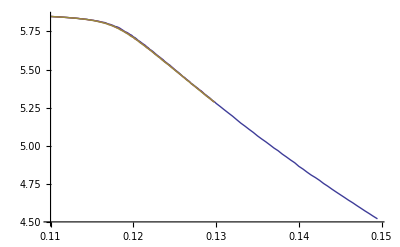

```mathematica
ListLinePlot[{avel10v6,avel20v6,avel30v6}]
```

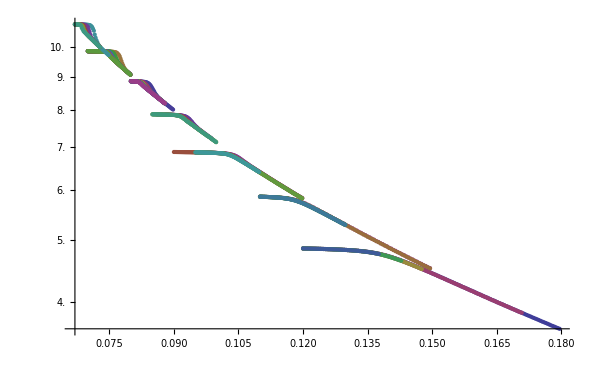

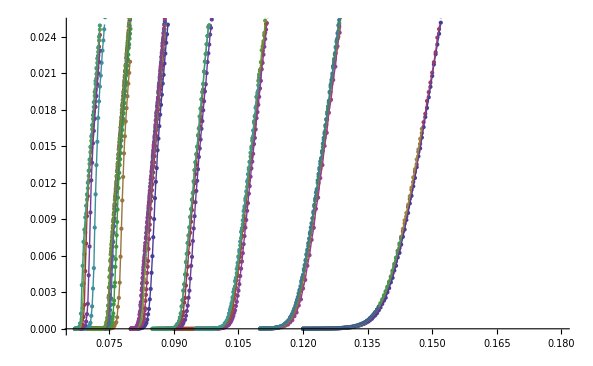

```mathematica
ListLogPlot[{avel5v5,avel10v5,avel20v5,avel30v5,avel50v5,avel5v6,avel10v6,avel20v6,avel30v6,avel5v7,avel10v7,avel20v7,avel30v7,avel5v8,avel10v8,avel20v8,avel20v8,avel5v9,avel10v9,avel20v9,avel30v9,avel40v9,avel50v9,avel5v10,avel10v10,avel20v10,avel30v10,avel40v10,avel50v10,avel5v11,avel10v11,avel20v11,avel30v11,avel50v11},PlotRange->Full]
pic1=ListPlot[{gap5v5,gap10v5,gap20v5,gap30v5,gap50v5,gap5v6,gap10v6,gap20v6,gap30v6,gap5v7,gap10v7,gap20v7,gap30v7,gap5v8,gap10v8,gap20v8,gap20v8,gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9,gap5v10,gap10v10,gap20v10,gap30v10,gap40v10,gap50v10,gap5v11,gap10v11,gap20v11,gap30v11,gap50v11},PlotRange->{Full,{0,0.025}}];
pic2=ListLinePlot[{gap5v5,gap10v5,gap20v5,gap30v5,gap50v5,gap5v6,gap10v6,gap20v6,gap30v6,gap5v7,gap10v7,gap20v7,gap30v7,gap5v8,gap10v8,gap20v8,gap20v8,gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9,gap5v10,gap10v10,gap20v10,gap30v10,gap40v10,gap50v10,gap5v11,gap10v11,gap20v11,gap30v11,gap50v11},PlotRange->{Full,{0,0.025}}];
Show[{pic1,pic2}]
```

```mathematica
gap1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gap1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10k1]}];
gap1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10k1]}];
gap1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10k1]}];
gap1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10k1]}];
gap1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g10k1]}];
gap1006=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g10k1]}];
gap1007=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g10k1]}];
gap1008=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g10k1]}];
```

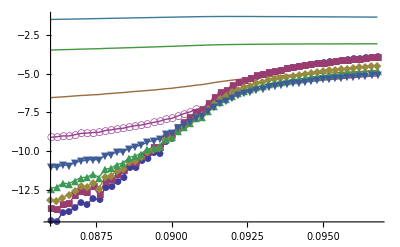

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008},PlotLegend->{"0","1","2","3","4","5","6","7","8"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full,PlotLabel->"GapDistribution, Vmax=8, 30k"]
```